# Bootstrapping v4.0 (smh)

## I mean at some point I am bound to get this right

```mathematica
ModuleDirectory = NotebookDirectory[] <> "../modules/";
<< (ModuleDirectory<> "debugTools.wl");
<< (ModuleDirectory<> "dataLoader.wl");
<< (ModuleDirectory<> "bootstraptdl.wl");
<< (ModuleDirectory<> "defect.wl");
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

```mathematica
?dataLoader`*
```

```mathematica
(* Calculate Transmissions in BDE *)
Module[
{md,s,z,weights,n,ind, out, sH, sR, bnd, M, L, B, r, cv, xv, cons, box, go},
md=ModularDataFoldZ2FixedMinimal[];
s=Get@FileNameJoin[{NotebookDirectory[],"S-matrix-su2xsu2-over-su2.m"}];
z=Get@FileNameJoin[{NotebookDirectory[],"DE-modular-invariant-su2xsu2-over-su2.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"conformal-weights-su2xsu2-over-su2.m"}];
 

n=Length@s;
ind=Pick[Range@n,Unitize@Diagonal@z,1]//Echo;
out=Complement[Range@n,ind];
sH=Conjugate@N[s,40];
sR=Re@N@s;
bnd=Table[Max[sR[[i,ind]]/sR[[1,ind]]],{i,n}];

(*integer lattice:(S*x)_out=0 and Im(S*x)_I=0*)
M=Join[Re@sH[[out]],Im@sH[[out]],Im@sH[[ind]]];
L=LatticeReduce@Join[IdentityMatrix@n,Round[10^25 Transpose@M],2];
B=Select[L,Norm@#[[n+1;;]]<10^10&][[All, ;;n]];
r=Length@B;

(*LP bounds on the lattice coefficients*)
cv=Array[c,r];
xv=cv.B;
cons=Join[Thread[xv>=0],Thread[xv<=bnd],Thread[sR[[ind]].xv>=0]];box=Table[{Ceiling[LinearOptimization[k,cons,cv,"PrimalMinimumValue"]-10^-6],Floor[-LinearOptimization[-k,cons,cv,"PrimalMinimumValue"]+10^-6]},{k,cv}];

(*depth-first search with LP pruning*)
(*go[fixed_]:=Module[{k=Length@fixed+1,cs,lo,hi},If[k>r,If[Min[sR[[ind]].(fixed.B)]>10^-6,Sow[fixed.B]],cs=Join[cons,MapThread[Equal,{cv[[;;k-1]],fixed}]];
lo=Quiet@LinearOptimization[cv[[k]],cs,cv,"PrimalMinimumValue"];
If[NumericQ@lo,hi=-LinearOptimization[-cv[[k]],cs,cv,"PrimalMinimumValue"];
Do[go[Append[fixed,j]],{j,Ceiling[lo-10^-6],Floor[hi+10^-6]}]]]];*)
]//Time
```

{1,3,4,6,8,10,12,14,15,17,34,36,37,39,41,43,45,47,48,50,67,69,70,72,74}

Time:   0.71724

```mathematica
(* Calculate Boundaries in C and Pull back to TIM^2 *)
Module[
{md,s, z, t,boundaries, defects, x, xz, pullbacks,untwisted,transmission,S,T,Z,weights,indices},
md=ModularDataFoldMinimal[];
s=Get@FileNameJoin[{NotebookDirectory[],"m-dcoset-sp6-S.m"}];
t=Get@FileNameJoin[{NotebookDirectory[],"m-dcoset-sp6-T.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"m-dcoset-sp6-conformal-weights.m"}];
weights//Echo;

(* The defects in here to find the inverse Z2 *)
defects= #/#[[1]] & /@ s//Simplify//Transpose;

boundaries = #/Sqrt[#[[1]]] & /@ s//Simplify//Transpose;

transmission=(a|->(1-#[[a]]/#[[1]])/2&/@boundaries )/@Range[Length@boundaries] ;
]//Time
```

{0,1/3,5/6,3/2,3/2,2,7/120,69/40,19/40,127/120,13/5,14/15,43/30,31/10,1/10,3/5,59/24,1/8,7/8,59/24,7/120,69/40,19/40,127/120,7/10,1/30,8/15,6/5,1/5,7/10,79/120,13/40,3/40,79/120,31/10,43/30,14/15,13/5,3/5,1/10}

Time:   1.86275

```mathematica
(* Calculate Boundaries in BAA and Pull back to TIM^2 *)
Module[
{md,s, z, t,boundaries, defects, x, xz, pullbacks,untwisted,transmission,S,T,Z,weights,indices},
md=ModularDataFoldMinimal[];
s=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-S-matrix.m"}];
t=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-T-matrix.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-conformal-weights.m"}];

(* The defects in here to find the inverse Z2 *)
defects= #/#[[1]] & /@ s//Simplify//Transpose;

S=Get@FileNameJoin[{NotebookDirectory[],"S-matrix-su2xsu2-over-su2.m"}];
T=Get@FileNameJoin[{NotebookDirectory[],"T-matrix-su2xsu2-over-su2.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"conformal-weights-su2xsu2-over-su2.m"}];
Z=Get@FileNameJoin[{NotebookDirectory[],"AE-modular-invariant-su2xsu2-over-su2.m"}];
indices=Get@FileNameJoin[{NotebookDirectory[],"index-convention-su2xsu2-over-su2.m"}];
indices//Echo;

boundaries = #/Sqrt[#[[1]]] & /@ S//Simplify//Transpose;

transmission=(1-#[[17]]/#[[1]])/2&/@boundaries;
transmission//N//Echo;
]//Time
```

{{0,0,0},{0,0,2},{0,0,4},{0,0,6},{0,0,8},{0,0,10},{0,1,1},{0,1,3},{0,1,5},{0,1,7},{0,1,9},{0,2,0},{0,2,2},{0,2,4},{0,2,6},{0,2,8},{0,2,10},{1,0,1},{1,0,3},{1,0,5},{1,0,7},{1,0,9},{1,1,0},{1,1,2},{1,1,4},{1,1,6},{1,1,8},{1,1,10},{1,2,1},{1,2,3},{1,2,5},{1,2,7},{1,2,9},{2,0,0},{2,0,2},{2,0,4},{2,0,6},{2,0,8},{2,0,10},{2,1,1},{2,1,3},{2,1,5},{2,1,7},{2,1,9},{2,2,0},{2,2,2},{2,2,4},{2,2,6},{2,2,8},{2,2,10},{3,0,1},{3,0,3},{3,0,5},{3,0,7},{3,0,9},{3,1,0},{3,1,2},{3,1,4},{3,1,6},{3,1,8},{3,1,10},{3,2,1},{3,2,3},{3,2,5},{3,2,7},{3,2,9},{4,0,0},{4,0,2},{4,0,4},{4,0,6},{4,0,8},{4,0,10},{4,1,1},{4,1,3},{4,1,5},{4,1,5}}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

Time:   3.24503

```mathematica
(* Calculate Boundaries in BAE and Pull back to TIM^2 *)
Module[
{md,s, z, t,boundaries, defects, x, xz, pullbacks,untwisted,transmission,S,T,Z,weights},
md=ModularDataFoldMinimal[];
s=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-S-matrix.m"}];
t=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-T-matrix.m"}];
weights=Get@FileNameJoin[{NotebookDirectory[],"AE-maximal-conformal-weights.m"}];
weights//Echo;

(* The defects in here to find the inverse Z2 *)
defects= #/#[[1]] & /@ s//Simplify//Transpose;

boundaries = #/Sqrt[#[[1]]] & /@ s//Simplify//Transpose;

transmission=(1-#[[5]]/#[[1]])/2&/@boundaries;
transmission//N//Echo;
]//Time
```

{0,3/2,7/8,3/2,2,61/80,21/80,61/80,21/80,6/5,7/10,3/40,7/10,1/5,1/16,9/16,1/16,9/16,3/5,1/10,19/40,19/40}

{0.,0.,0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,0.,0.,1.,1.,1.,1.,0.,0.,0.,0.}

Time:   0.073893

{0,3/80,7/160,1/16,3/40,3/32,1/10,11/80,1/5,21/80,11/32,7/16,19/40,43/80,9/16,19/32,3/5,51/80,7/10,61/80,127/160,27/32,7/8,83/80,43/40,6/5,6/5,207/160,3/2,123/80,247/160,8/5,15/8,31/16,2,21/10,11/5,3,4}

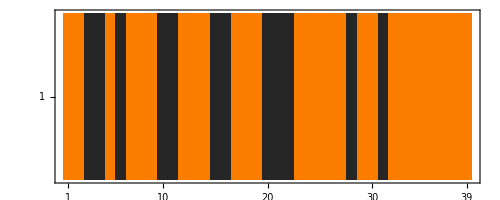

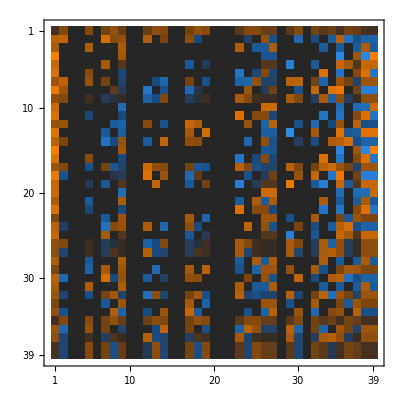

Time:   3.04429

{0,0,1,1,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0}

```mathematica
(* Calculate Boundaries in TIM^2/Z_2 and Pull back to TIM^2 *)
Module[
{md,s, z, t,boundaries, defects, x, xz, pullbacks,untwisted,transmission},
md=ModularDataFoldZ2OrbifoldMinimal[];
s=md["S"];
t=md["T"];
z=md["Z"];
md["irreps"]["weights"] //Echo;

(* Calculate boundaries *)
boundaries = #/Sqrt[#[[1]]] & /@ s//Simplify//Transpose;
(*boundaries//MatrixPlot//Echo;*)

(* The defects in here to find the inverse Z2 *)
defects= #/#[[1]] & /@ s//Simplify//Transpose;
(*defects//MatrixForm//Echo;*)

(* It looks like there are 3 Z_2's in there in a Z_2^2, 
   so which one is the inverse? 
(probably the diagonal one) *)
x = defects[[-5]];

(* Let's check if it is *)
xz = x*#&/@z;
(z + xz + s . xz . s + t . s . xz . s . ConjugateTranspose[t])/2// N//Chop // MatrixPlot/Echo;
(* Ok it isn't the last one, but it is the one I picked because I now have checked lol *)

(*The pullback is going to be *)
pullbacks = (# + x * #)/Sqrt[2]&/@ boundaries //Simplify;
untwisted =If[Abs[#[[3]]]<2,1,0]&/@md["irreps"]["labels"];
{untwisted}//MatrixPlot//Echo;
Select[pullbacks,# * untwisted== #&]//MatrixPlot//Echo;
transmission=(1-#[[-5]]/#[[1]])/2&/@Select[pullbacks,#*untwisted==#&]
]//Time
```

```mathematica
md = ModularDataFoldZ2FixedMinimal[] // Time;
mb = ModularBootstrapTraces[md,20] //Time;
traces = mb["defects"] // ToRoots//Time;
qdim = Transpose[traces][[1]];
r=Length@qdim;
traces //Transpose // MatrixForm
```

Time:   0.086401

Time:   1.93894

Time:   0.239237

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | √5 | -√5 | 0 | 1 | -1 | 0 | 0 | -√(3-√5) | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | √(3-√5) | -√(3-√5) | √(3-√5) | -√(3-√5) | 0 | 0 | 3-√5 | -3+√5 | 0 | √(7-3 √5) | -√(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | 0 | 3+√5 | -3-√5 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | -√5 | √5 | 0 | 1 | -1 | 0 | 0 | -√(3+√5) | -√(3-√5) | √(3-√5) | √(3+√5) | 0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 2 √2 | 2 √2 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | -√(3-√5) | √(3-√5) | -√(3-√5) | √(3-√5) | 0 | 0 | 3-√5 | -3+√5 | 0 | -√(7-3 √5) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 0 | 1-√5 | 1-√5 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | -2+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | -√5 | √5 | 0 | 1 | -1 | 0 | 0 | √(3+√5) | √(3-√5) | -√(3-√5) | -√(3+√5) | 0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 0 | 1+√5 | 1+√5 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | √5 | -√5 | 0 | 1 | -1 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) | -√(3-√5) | 0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | -2 √2 | -2 √2 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | 0 | 3+√5 | -3-√5 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5)))

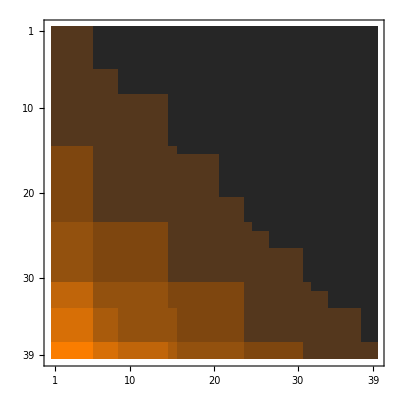
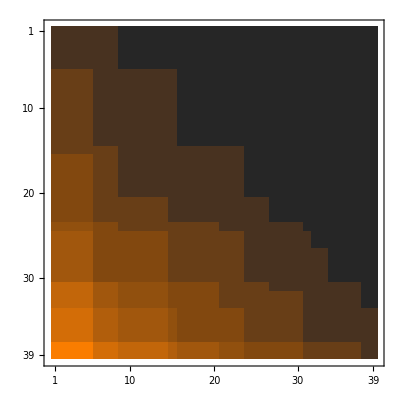
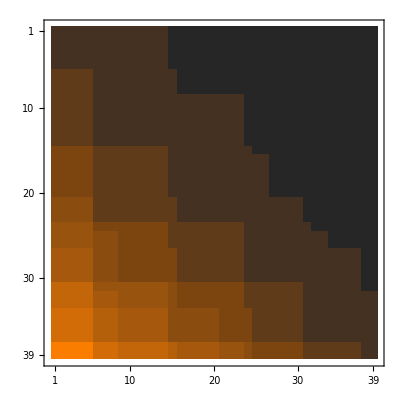
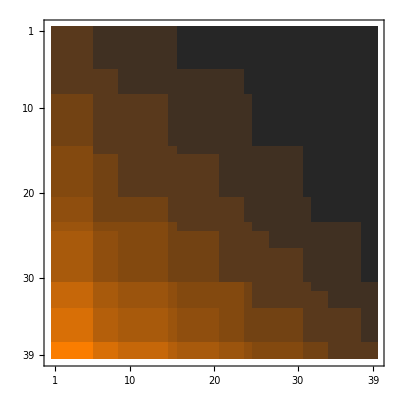
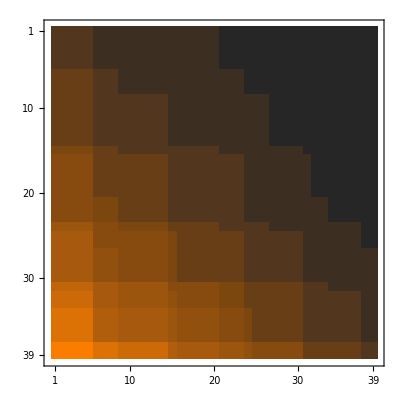
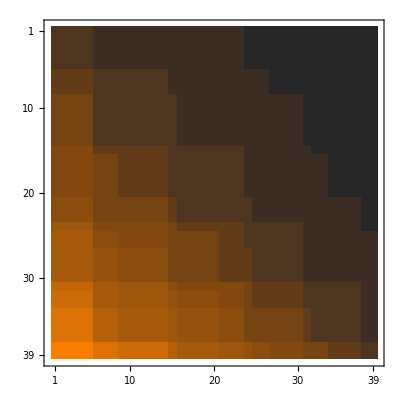
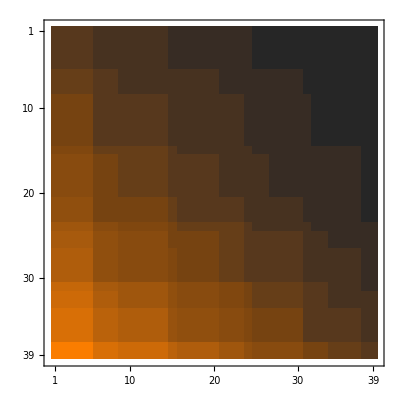
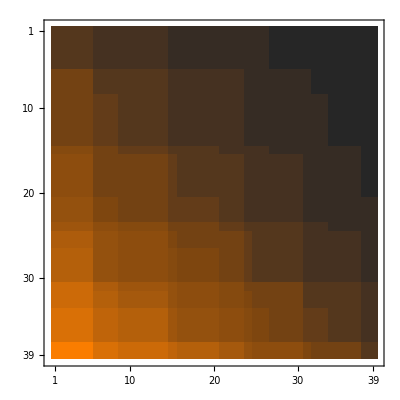
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
B=Array[Floor@N[qdim[[#1]]qdim[[#2]]/qdim[[#3]]] &, {r,r,r}];
MatrixPlot /@B
```

```mathematica
traces
```

{{1,1,0,-1,-1,2,0,1,1,0,-2,0,2,0,2,-1,-1,0,-1,-1,1,1,1,1,2,0,2,-1,-1,0,1,1,2,1,1,1,1,1,1},{1,-1,0,1,-1,0,0,1,-1,0,0,0,0,0,0,1,-1,0,-1,1,-1,1,1,-1,0,0,0,-1,1,0,-1,1,0,-1,1,1,-1,-1,1},{1,1,-2,1,1,2,-2,1,1,-2,2,-2,2,-2,2,1,1,-2,1,1,1,1,1,1,2,-2,2,1,1,-2,1,1,2,1,1,1,1,1,1},{1,1,2,1,1,2,2,1,1,2,2,2,2,2,2,1,1,2,1,1,1,1,1,1,2,2,2,1,1,2,1,1,2,1,1,1,1,1,1},{1,-1,0,-1,1,0,0,1,-1,0,0,0,0,0,0,-1,1,0,1,-1,-1,1,1,-1,0,0,0,1,-1,0,-1,1,0,-1,1,1,-1,-1,1},{√2,√2,√2,0,0,0,-√2,-√2,-√2,√2,0,-√2,2 √2,√2,0,0,0,√2,0,0,-√2,-√2,√2,√2,0,-√2,-2 √2,0,0,-√2,√2,√2,0,√2,√2,-√2,-√2,-√2,-√2},{√2,√2,-√2,0,0,0,√2,-√2,-√2,-√2,0,√2,2 √2,-√2,0,0,0,-√2,0,0,-√2,-√2,√2,√2,0,√2,-2 √2,0,0,√2,√2,√2,0,√2,√2,-√2,-√2,-√2,-√2},{√2,-√2,0,0,0,0,0,-√2,√2,0,0,0,0,0,0,0,0,0,0,0,√2,-√2,√2,-√2,0,0,0,0,0,0,-√2,√2,0,-√2,√2,-√2,√2,√2,-√2},{1/2 (1+√5),1/2 (1+√5),√5,1/2 (-1+√5),1/2 (-1+√5),1,0,1/2 (1-√5),1/2 (1-√5),0,-1,-√5,1,0,1-√5,1/2 (-1-√5),1/2 (-1-√5),-√5,1/2 (-1+√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,√5,1,1/2 (-1-√5),1/2 (-1-√5),0,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (1+√5),-√5,1/2 (-1+√5),1/2 (-1+√5),1,0,1/2 (1-√5),1/2 (1-√5),0,-1,√5,1,0,1-√5,1/2 (-1-√5),1/2 (-1-√5),√5,1/2 (-1+√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,-√5,1,1/2 (-1-√5),1/2 (-1-√5),0,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (-1-√5),0,1/2 (1-√5),1/2 (-1+√5),0,0,1/2 (1-√5),1/2 (-1+√5),0,0,0,0,0,0,1/2 (1+√5),1/2 (-1-√5),0,1/2 (-1+√5),1/2 (1-√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (-1+√5),0,0,0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (-1+√5),1/2 (1-√5),1/2 (1+√5),1/2 (-1-√5),1/2 (-1-√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1,1-√5,1/2 (1-√5),1/2 (1-√5),1+√5,1,1,1,1-√5,1-√5,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,1,1,1/2 (1+√5),1/2 (1+√5),1+√5,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (1+√5),-1,1/2 (1-√5),1/2 (1-√5),1,-1+√5,1/2 (1-√5),1/2 (1-√5),-1-√5,1,-1,1,-1+√5,1-√5,1/2 (1+√5),1/2 (1+√5),-1,1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1/2 (1-√5),1+√5,-1,1,1/2 (1+√5),1/2 (1+√5),-1-√5,1/2 (1+√5),1/2 (1+√5),1,1/2 (1-√5),1/2 (1-√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5),1/2 (1+√5)},{1/2 (1+√5),1/2 (-1-√5),0,1/2 (-1+√5),1/2 (1-√5),0,0,1/2 (1-√5),1/2 (-1+√5),0,0,0,0,0,0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (1-√5),1/2 (-1+√5),1/2 (-1+√5),1/2 (1-√5),1/2 (1-√5),1/2 (-1+√5),0,0,0,1/2 (1+√5),1/2 (-1-√5),0,1/2 (-1-√5),1/2 (1+√5),0,1/2 (-1+√5),1/2 (1-√5),1/2 (1+√5),1/2 (-1-√5),1/2 (-1-√5),1/2 (1+√5)},{2,2,0,0,0,-4,0,2,2,0,0,0,4,0,-4,0,0,0,0,0,2,2,2,2,-4,0,4,0,0,0,2,2,-4,2,2,2,2,2,2},{√(3+√5),√(3+√5),-√(3-√5),0,0,-√10,√(3-√5),√(3-√5),√(3-√5),√(3+√5),0,-√(3+√5),√2,-√(3-√5),0,0,0,√(3+√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,√(3-√5),-√2,0,0,-√(3+√5),√(3+√5),√(3+√5),√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),√(3+√5),-√(3+√5),0,0,√10,-√(3-√5),√(3-√5),√(3-√5),-√(3+√5),0,-√(3-√5),√2,√(3-√5),0,0,0,√(3-√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,√(3+√5),-√2,0,0,√(3+√5),√(3+√5),√(3+√5),-√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),√(3+√5),√(3+√5),0,0,√10,√(3-√5),√(3-√5),√(3-√5),√(3+√5),0,√(3-√5),√2,-√(3-√5),0,0,0,-√(3-√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,-√(3+√5),-√2,0,0,-√(3+√5),√(3+√5),√(3+√5),-√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),√(3+√5),√(3-√5),0,0,-√10,-√(3-√5),√(3-√5),√(3-√5),-√(3+√5),0,√(3+√5),√2,√(3-√5),0,0,0,-√(3+√5),0,0,√(3-√5),√(3-√5),-√(3-√5),-√(3-√5),0,-√(3-√5),-√2,0,0,√(3+√5),√(3+√5),√(3+√5),√10,-√(3-√5),-√(3-√5),-√(3+√5),-√(3+√5),-√(3+√5),-√(3+√5)},{√(3+√5),-√(3+√5),0,0,0,0,0,√(3-√5),-√(3-√5),0,0,0,0,0,0,0,0,0,0,0,-√(3-√5),√(3-√5),-√(3-√5),√(3-√5),0,0,0,0,0,0,-√(3+√5),√(3+√5),0,√(3-√5),-√(3-√5),-√(3+√5),√(3+√5),√(3+√5),-√(3+√5)},{1/2 (3+√5),1/2 (3+√5),0,1/2 (-3+√5),1/2 (-3+√5),-2,0,1/2 (3-√5),1/2 (3-√5),0,2,0,-2,0,3-√5,1/2 (-3-√5),1/2 (-3-√5),0,1/2 (-3+√5),1/2 (-3+√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),3+√5,0,-2,1/2 (-3-√5),1/2 (-3-√5),0,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5)},{1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),-2,3-√5,1/2 (3-√5),1/2 (3-√5),3+√5,-2,-2,-2,3-√5,3-√5,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),3+√5,-2,-2,1/2 (3+√5),1/2 (3+√5),3+√5,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5)},{1/2 (3+√5),1/2 (3+√5),2,1/2 (3-√5),1/2 (3-√5),-2,-3+√5,1/2 (3-√5),1/2 (3-√5),-3-√5,-2,2,-2,-3+√5,3-√5,1/2 (3+√5),1/2 (3+√5),2,1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),1/2 (3-√5),3+√5,2,-2,1/2 (3+√5),1/2 (3+√5),-3-√5,1/2 (3+√5),1/2 (3+√5),-2,1/2 (3-√5),1/2 (3-√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5),1/2 (3+√5)},{1+√5,1+√5,0,0,0,-2,0,1-√5,1-√5,0,0,0,2,0,-2+2 √5,0,0,0,0,0,1-√5,1-√5,1-√5,1-√5,-2-2 √5,0,2,0,0,0,1+√5,1+√5,-2,1-√5,1-√5,1+√5,1+√5,1+√5,1+√5},{√(7+3 √5),√(7+3 √5),√2,0,0,0,√(7-3 √5),-√(7-3 √5),-√(7-3 √5),-√(7+3 √5),0,-√2,-2 √2,-√(7-3 √5),0,0,0,√2,0,0,-√(7-3 √5),-√(7-3 √5),√(7-3 √5),√(7-3 √5),0,-√2,2 √2,0,0,√(7+3 √5),√(7+3 √5),√(7+3 √5),0,√(7-3 √5),√(7-3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5)},{√(7+3 √5),√(7+3 √5),-√2,0,0,0,-√(7-3 √5),-√(7-3 √5),-√(7-3 √5),√(7+3 √5),0,√2,-2 √2,√(7-3 √5),0,0,0,-√2,0,0,-√(7-3 √5),-√(7-3 √5),√(7-3 √5),√(7-3 √5),0,√2,2 √2,0,0,-√(7+3 √5),√(7+3 √5),√(7+3 √5),0,√(7-3 √5),√(7-3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5),-√(7+3 √5)},{√(2 (5+√5)),-√(2 (5+√5)),0,-√(5-√5),√(5-√5),0,0,√(2 (5-√5)),-√(2 (5-√5)),0,0,0,0,0,0,-√(5+√5),√(5+√5),0,-√(5-√5),√(5-√5),√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),-√(2 (5-√5)),0,0,0,-√(5+√5),√(5+√5),0,√(2 (5+√5)),-√(2 (5+√5)),0,√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),-√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5))},{√(2 (5+√5)),-√(2 (5+√5)),0,√(5-√5),-√(5-√5),0,0,√(2 (5-√5)),-√(2 (5-√5)),0,0,0,0,0,0,√(5+√5),-√(5+√5),0,√(5-√5),-√(5-√5),√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),-√(2 (5-√5)),0,0,0,√(5+√5),-√(5+√5),0,√(2 (5+√5)),-√(2 (5+√5)),0,√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),-√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5))},{√(2 (5+√5)),√(2 (5+√5)),0,√(5-√5),√(5-√5),0,0,√(2 (5-√5)),√(2 (5-√5)),0,0,0,0,0,0,√(5+√5),√(5+√5),0,-√(5-√5),-√(5-√5),-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),√(2 (5-√5)),0,0,0,-√(5+√5),-√(5+√5),0,-√(2 (5+√5)),-√(2 (5+√5)),0,-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5)),-√(2 (5+√5))},{√(2 (5+√5)),√(2 (5+√5)),0,-√(5-√5),-√(5-√5),0,0,√(2 (5-√5)),√(2 (5-√5)),0,0,0,0,0,0,-√(5+√5),-√(5+√5),0,√(5-√5),√(5-√5),-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5-√5)),√(2 (5-√5)),0,0,0,√(5+√5),√(5+√5),0,-√(2 (5+√5)),-√(2 (5+√5)),0,-√(2 (5-√5)),-√(2 (5-√5)),√(2 (5+√5)),√(2 (5+√5)),-√(2 (5+√5)),-√(2 (5+√5))},{3+√5,3+√5,0,0,0,4,0,3-√5,3-√5,0,0,0,-4,0,-6+2 √5,0,0,0,0,0,3-√5,3-√5,3-√5,3-√5,-6-2 √5,0,-4,0,0,0,3+√5,3+√5,4,3-√5,3-√5,3+√5,3+√5,3+√5,3+√5},{2 √(5+√5),-2 √(5+√5),0,0,0,0,0,-2 √(5-√5),2 √(5-√5),0,0,0,0,0,0,0,0,0,0,0,-2 √(5-√5),2 √(5-√5),2 √(5-√5),-2 √(5-√5),0,0,0,0,0,0,2 √(5+√5),-2 √(5+√5),0,2 √(5-√5),-2 √(5-√5),-2 √(5+√5),2 √(5+√5),-2 √(5+√5),2 √(5+√5)},{2 √(5+√5),2 √(5+√5),0,0,0,0,0,-2 √(5-√5),-2 √(5-√5),0,0,0,0,0,0,0,0,0,0,0,2 √(5-√5),2 √(5-√5),2 √(5-√5),2 √(5-√5),0,0,0,0,0,0,-2 √(5+√5),-2 √(5+√5),0,-2 √(5-√5),-2 √(5-√5),-2 √(5+√5),-2 √(5+√5),2 √(5+√5),2 √(5+√5)},{2 √(5+2 √5),2 √(5+2 √5),0,-√(2 (5-2 √5)),-√(2 (5-2 √5)),0,0,-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,0,0,0,√(2 (5+2 √5)),√(2 (5+2 √5)),0,√(2 (5-2 √5)),√(2 (5-2 √5)),2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,-√(2 (5+2 √5)),-√(2 (5+2 √5)),0,-2 √(5+2 √5),-2 √(5+2 √5),0,2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5),-2 √(5+2 √5)},{2 √(5+2 √5),2 √(5+2 √5),0,√(2 (5-2 √5)),√(2 (5-2 √5)),0,0,-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,0,0,0,-√(2 (5+2 √5)),-√(2 (5+2 √5)),0,-√(2 (5-2 √5)),-√(2 (5-2 √5)),2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),-2 √(5-2 √5),0,0,0,√(2 (5+2 √5)),√(2 (5+2 √5)),0,-2 √(5+2 √5),-2 √(5+2 √5),0,2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5),-2 √(5+2 √5)},{2 √(5+2 √5),-2 √(5+2 √5),0,√(2 (5-2 √5)),-√(2 (5-2 √5)),0,0,-2 √(5-2 √5),2 √(5-2 √5),0,0,0,0,0,0,-√(2 (5+2 √5)),√(2 (5+2 √5)),0,√(2 (5-2 √5)),-√(2 (5-2 √5)),-2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),2 √(5-2 √5),0,0,0,-√(2 (5+2 √5)),√(2 (5+2 √5)),0,2 √(5+2 √5),-2 √(5+2 √5),0,-2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),-2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5)},{2 √(5+2 √5),-2 √(5+2 √5),0,-√(2 (5-2 √5)),√(2 (5-2 √5)),0,0,-2 √(5-2 √5),2 √(5-2 √5),0,0,0,0,0,0,√(2 (5+2 √5)),-√(2 (5+2 √5)),0,-√(2 (5-2 √5)),√(2 (5-2 √5)),-2 √(5-2 √5),2 √(5-2 √5),-2 √(5-2 √5),2 √(5-2 √5),0,0,0,√(2 (5+2 √5)),-√(2 (5+2 √5)),0,2 √(5+2 √5),-2 √(5+2 √5),0,-2 √(5-2 √5),2 √(5-2 √5),2 √(5+2 √5),-2 √(5+2 √5),2 √(5+2 √5),-2 √(5+2 √5)},{2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),0,0,0,0,0,2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),0,0,0,0,0,0,0,0,0,0,0,2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),0,0,0,0,0,0,2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),0,-2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),-2 √(2 (5+2 √5)),2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),2 √(2 (5+2 √5))},{2 √(2 (5+2 √5)),2 √(2 (5+2 √5)),0,0,0,0,0,2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),0,0,0,0,0,0,0,0,0,0,0,-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),-2 √(2 (5-2 √5)),0,0,0,0,0,0,-2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),0,2 √(2 (5-2 √5)),2 √(2 (5-2 √5)),-2 √(2 (5+2 √5)),-2 √(2 (5+2 √5)),2 √(2 (5+2 √5)),2 √(2 (5+2 √5))}}

```mathematica
AA=Select[traces//Transpose,#[[4]]!=2&];
vals=Union[Flatten[AA]];
field=ToNumberField[vals,All];
A=AA/. Thread[vals->field];
x=Array[x,r];
F= [A];
```

Part::partd: Part specification traces⟦4⟧ is longer than depth of object.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

ToNumberField::nalg: Transpose[] is not an explicit algebraic number.

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[x,r].

```mathematica
{i,j}={38,4};
b=A[[All,i]]*A[[All,j]];
M=B[[i,j]];
F[b]//Chop//Rationalize//Time
x/.#& /@Solve[Thread[A . x == b]~Join~Thread[ 0<= x <= M],x,Integers]
```

Time:   0.000319

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}}

```mathematica
A//FullSimplify//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
-1 | -1 | 1 | 1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
-1 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | -1 | 1 | 1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5))

```mathematica
PolynomialCoefficients[x_]:=PolynomialCoefficients[x]=CoefficientList[MinimalPolynomial[x,y],y];
NumericalValue[x_]  := Round[N[x,40]*10^30];
ParseEntry[i_,j_]:=Module[
{coefficients = PolynomialCoefficients[AA[[i,j]]]},
{i,j,Length[coefficients]-1, coefficients, NumericalValue[AA[[i,j]]]}
];
Aexport=Flatten[Array[ParseEntry,Dimensions[AA]],1];//Time
Export[ModuleDirectory<>"fusion/in/A.txt", Aexport]
```

Time:   0.39291

/home/pano/projects/tricritical-ising/bootstrap/scratch/../modules/fusion/in/A.txt

/home/pano/projects/tricritical-ising/bootstrap/scratch/../modules/fusion/in/A.txt

```mathematica
AA=Get@FileNameJoin[{NotebookDirectory[],"S-matrix-su2xsu2-over-su2.m"}] // FullSimplify;
(*AA=#/#[[1]] &/@ AA//FullSimplify*)
```

```mathematica
ToFile[AA,ModuleDirectory<>"fusion/in/A.txt", 30];
```